```mathematica
dat = {{-1/2*{l^4-4*l^3-2*l^2-4*l-1}*{l-1}/{l^4-1},1.46557123187677,2},{-1/2*{l^4-2*l^3-2*l+1}*{l-1}/{l^4-1},1.46557123187677,2},{-1/2*{l^4-6*l^3-2*l^2-2*l-5}*{l-1}/{l^4-1},1.61803398874989,2},{-1/2*{l^4-4*l^3-4*l^2-2*l-1}*{l-1}/{l^4-1},1.61803398874989,2},{-1/2*{l^3-4*l^2-4*l-1}*{l-1}/{l^3-1},1.61803398874989,2},{-1/2*{l^4-4*l^3-3}*{l-1}/{l^4-1},1.61803398874989,2},{-1/2*{l^4-2*l^3-2*l^2+1}*{l-1}/{l^4-1},1.61803398874989,2},{-1/2*{l^3-2*l^2-2*l+1}*{l-1}/{l^3-1},1.61803398874989,2},{-1/2*{l^4-6*l^3-4*l^2-4*l-3}*{l-1}/{l^4-1},1.00000000000000,2},{-1/2*{l^4-6*l^3-4*l^2-2*l-5}*{l-1}/{l^4-1},1.00000000000000,2},{-1/2*{l^3-6*l^2-4*l-3}*{l-1}/{l^3-1},1.00000000000000,2},{-1/2*{l^3-6*l^2-2*l-5}*{l-1}/{l^3-1},1.00000000000000,2},{-1/2*{l^4-6*l^3-2*l^2-4*l-5}*{l-1}/{l^4-1},1.00000000000000,2},{-1/2*{l^4-4*l^3-4*l^2-2*l-3}*{l-1}/{l^4-1},1.00000000000000,2},{-1/2*{l^4-4*l^3-2*l^2-2*l-1}*{l-1}/{l^4-1},1.00000000000000,2},{-1/2*{l^4-4*l^3-2*l^2-3}*{l-1}/{l^4-1},1.00000000000000,2},{-1/2*{l^3-4*l^2-2*l-1}*{l-1}/{l^3-1},1.00000000000000,2},{-1/2*{l^3-4*l^2-3}*{l-1}/{l^3-1},1.00000000000000,2},{-1/2*{l^4-4*l^3-2*l-3}*{l-1}/{l^4-1},1.00000000000000,2},{-1/2*{l^4-2*l^3-2*l^2-1}*{l-1}/{l^4-1},1.00000000000000,2},{-1/2*{l^4-6*l^3-2*l^2-2*l-3}*{l-1}/{l^4-1},1.83928675521416,2},{-1/2*{l^4-4*l^3-4*l^2-4*l-1}*{l-1}/{l^4-1},1.83928675521416,2},{-1/2*{l^4-4*l^3-1}*{l-1}/{l^4-1},1.83928675521416,2},{-1/2*{l^4-2*l^3-2*l^2-2*l+1}*{l-1}/{l^4-1},1.83928675521416,2},{-1/2*{l^3-6*l^2-2*l-3}*{l-1}/{l^3-1},1.61803398874989,2},{-1/2*{l^3-4*l^2-1}*{l-1}/{l^3-1},1.61803398874989,2},{-1/2*{l^4-6*l^3-2*l^2-4*l-3}*{l-1}/{l^4-1},1.46557123187677,2},{-1/2*{l^4-4*l^3-2*l-1}*{l-1}/{l^4-1},1.46557123187677,2},{-1/2*{l^2-6*l-3}*{l-1}/{l^2-1},1.00000000000000,2},{-1/2*{l^2-4*l-1}*{l-1}/{l^2-1},1.00000000000000,2},{-1/2*{l^4-2*l^3-1}*{l-1}/{l^4-1},1.00000000000000,2},{-1/2*{l^3-2*l^2-1}*{l-1}/{l^3-1},1.00000000000000,2},{-1/2*{l^2-2*l-1}*{l-1}/{l^2-1},1.00000000000000,2},{-1/2*{l^3-2*l^2-2*l-1}*{l-1}/{l^3-1},1.00000000000000,2},{-1/2*{l^4-2*l^3-2*l^2-2*l-1}*{l-1}/{l^4-1},1.00000000000000,2},{-1/2*l+3/2,1.00000000000000,2},{-1/2*{l^4-4*l^3-2*l^2-2*l-3}*{l-1}/{l^4-1},1.00000000000000,2},{-1/2*{l^3-4*l^2-2*l-3}*{l-1}/{l^3-1},1.00000000000000,2},{-1/2*{l^2-4*l-3}*{l-1}/{l^2-1},1.00000000000000,2},{-1/2*{l^3-4*l^2-4*l-3}*{l-1}/{l^3-1},1.00000000000000,2},{-1/2*{l^4-4*l^3-4*l^2-4*l-3}*{l-1}/{l^4-1},1.00000000000000,2},{-1/2*l+5/2,1.00000000000000,2}};
```

```mathematica
r = ReflectionTransform[{-1,1}];
```

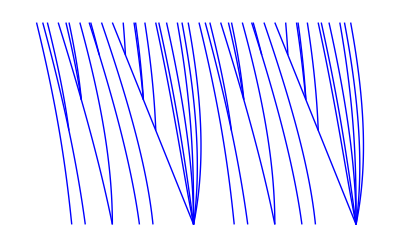

```mathematica
Show[
(Plot[#⟦1⟧,{l,#⟦2⟧,#⟦3⟧}]&/@dat)/.L_Line:>{Blue,GeometricTransformation[L,r]},
PlotRange->All,
Axes->False]
```

```mathematica
dat2 = {{1/2*{l^4+4*l^2+2*l+1}*{l-1}/{l^4-1},1.00000000000000,2},{1/2*{l^3+4*l+1}*{l-1}/{l^3-1},1.00000000000000,2},{1/2*{l^4+2*l^2+4*l+1}*{l-1}/{l^4-1},1.00000000000000,2},{1/2*{l^3+2*l+3}*{l-1}/{l^3-1},1.00000000000000,2},{1/2*{l^4+2*l^2+2*l+3}*{l-1}/{l^4-1},1.00000000000000,2},{1/2*{l^4-2*l^3+2*l^2-1}*{l-1}/{l^4-1},1.00000000000000,2},{1/2*{l^3-2*l^2+2*l-1}*{l-1}/{l^3-1},1.00000000000000,2},{1/2*{l^4-2*l^3+2*l-1}*{l-1}/{l^4-1},1.00000000000000,2},{1/2*{l^3-2*l^2+1}*{l-1}/{l^3-1},1.00000000000000,2},{1/2*{l^4-2*l^3+1}*{l-1}/{l^4-1},1.00000000000000,2},{1/2*{l^3+2*l^2+2*l+5}*{l-1}/{l^3-1},1.61803398874989,2},{1/2*{l^4+2*l^3+2*l^2+4*l+5}*{l-1}/{l^4-1},1.61803398874989,2},{1/2*{l^4+4*l^2+4*l+1}*{l-1}/{l^4-1},1.61803398874989,2},{1/2*{l^3+3}*{l-1}/{l^3-1},1.61803398874989,2},{1/2*{l^4+2*l+3}*{l-1}/{l^4-1},1.61803398874989,2},{1/2*{l^4-2*l^3+2*l^2+2*l-1}*{l-1}/{l^4-1},1.61803398874989,2},{1/2*{l^4+2*l^3+2*l^2+2*l+5}*{l-1}/{l^4-1},1.83928675521416,2},{1/2*{l^4+4*l^2+4*l+3}*{l-1}/{l^4-1},1.83928675521416,2},{1/2*{l^4+3}*{l-1}/{l^4-1},1.83928675521416,2},{1/2*{l^4-2*l^3+2*l^2+2*l+1}*{l-1}/{l^4-1},1.83928675521416,2},{1/2*{l^3+4*l+3}*{l-1}/{l^3-1},1.61803398874989,2},{1/2*{l^3-2*l^2+2*l+1}*{l-1}/{l^3-1},1.61803398874989,2},{1/2*{l^4+2*l^3+4*l^2+2*l+5}*{l-1}/{l^4-1},1.46557123187677,2},{1/2*{l^4+4*l^2+2*l+3}*{l-1}/{l^4-1},1.46557123187677,2},{1/2*{l^4+2*l^2+3}*{l-1}/{l^4-1},1.46557123187677,2},{1/2*{l^4-2*l^3+2*l^2+1}*{l-1}/{l^4-1},1.46557123187677,2},{1/2*{l^4+2*l^3+2*l^2+4*l+3}*{l-1}/{l^4-1},1.00000000000000,2},{1/2*{l^2+3}*{l-1}/{l^2-1},1.00000000000000,2},{1/2*{l^4+2*l+1}*{l-1}/{l^4-1},1.00000000000000,2},{1/2*{l^2-2*l+1}*{l-1}/{l^2-1},1.00000000000000,2},{1/2*l-1/2,1.00000000000000,2},{1/2*{l^4+1}*{l-1}/{l^4-1},1.00000000000000,2},{1/2*{l^3+1}*{l-1}/{l^3-1},1.00000000000000,2},{1/2*{l^2+1}*{l-1}/{l^2-1},1.00000000000000,2},{1/2*{l^3+2*l+1}*{l-1}/{l^3-1},1.00000000000000,2},{1/2*{l^4+2*l^2+2*l+1}*{l-1}/{l^4-1},1.00000000000000,2},{1/2*l+1/2,1.00000000000000,2},{1/2*{l^4+2*l^3+2*l^2+2*l+3}*{l-1}/{l^4-1},1.00000000000000,2},{1/2*{l^3+2*l^2+2*l+3}*{l-1}/{l^3-1},1.00000000000000,2},{1/2*{l^2+2*l+3}*{l-1}/{l^2-1},1.00000000000000,2},{1/2*{l^3+2*l^2+4*l+3}*{l-1}/{l^3-1},1.00000000000000,2},{1/2*{l^4+2*l^3+4*l^2+4*l+3}*{l-1}/{l^4-1},1.00000000000000,2}};
```

```mathematica
r = ReflectionTransform[{-1,1}];
```

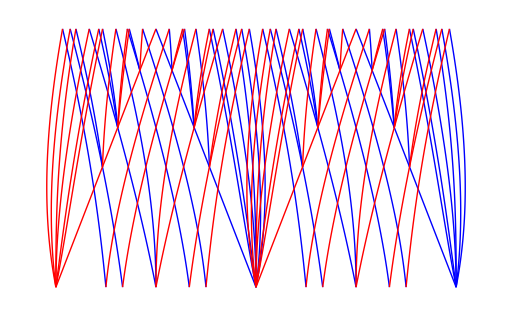

```mathematica
t = {Plot[#⟦1⟧,{l,#⟦2⟧,#⟦3⟧}]&/@dat,
Plot[#⟦1⟧,{l,#⟦2⟧,#⟦3⟧}]&/@dat2};
Show[t⟦1⟧/.L_Line:>{Blue,GeometricTransformation[L,r]},t⟦2⟧/.L_Line :> {Red, GeometricTransformation[L,r]},
PlotRange->All,
Axes->False]
```

```mathematica
Solve[x^2-x-1==0,x]//N
```

{{x→-0.618034},{x→1.61803}}

```mathematica
(1/18*Sqrt[31]*Sqrt[3]+29/54)^(1/3)+1/9/(1/18*Sqrt[31]*Sqrt[3]+29/54)^(1/3)+1/3//FullSimplify
```

Root[-1-#1^2+#1^3&,1]

```mathematica
Reduce[-1/2*(l^5-2*l^4-2*l^2+2*l-1)*(l-1)/(l^5-1)
==-1/2*(l^6-2*l^5-2*l^3+2*l^2-2*l+1)*(l-1)/(l^6-1)]//N
```

l==1.4036||l==-0.656781-0.837593 ⅈ||l==-0.656781+0.837593 ⅈ||l==0.45498-0.649504 ⅈ||l==0.45498+0.649504 ⅈ